## Comparing linear functions

### Isabella and Henry's pools

Isabella filled a 200-liter pool and Henry filled a 250-liter pool. They both started at the same time.

The following equation gives the volume of water in Isabella's pool (in liters) as a function of time (in minutes):

```mathematica
V=23t
```

23 t

The graph of the volume of water in Henry's pool (in liters) as a function of time (in minutes) is shown below.

Who filled their pool at a faster rate?

Who filled their entire pool first?

```mathematica
x="Minutes";y="Liters";x1=0; y1=0; x2=1;y2=25; x3=10; y3=300;
ListLinePlot[{{x1,y1},{x2,y2},{x3,y3}},GridLines->{
Range[0,10,1],
Range[0,300,25]},AxesStyle->Arrowheads[0.05],PlotStyle->Green,AxesLabel->{x,y},AspectRatio->1]
```

-Graphics-

The rate at which Isabella filled her pool is represented by the slope of the graph of V=23t. Since the formula for V is in slope-intercept form, we can determine that the slope is 23. This means that Isabella filled her pool at a rate of 23 liters per minute.

The rate at which Henry filled his pool is represented by the slope of the line on the graph. The line passes through the points (0,0) and (1,25). We can find its slope by taking the ratio of the corresponding differences in the y-values and the x-values of our two points:

```mathematica
(y2-y1)/(x2-x1)
```

25

Since 23<25, Henry filled his pool faster.

The size of Isabella's pool is 200 liters, so the time it took her to fill the entire pool corresponds to the value of t when V=200. We can find it by using the formula for V and solving the resulting equation:

```mathematica
Solve[V==23t/.V->200]
```

{{t→200/23}}

This means it took Isabella 8+16/23 minutes to fill her entire pool.

The size of Henry's pool is 250 liters, so the time it took him to fill the entire pool corresponds to the point on the graph whose y-value is 250, which is (10,250). This means it took Henry 10 minutes to fill his entire pool.

Since 8+16/23 < 10, Isabella filled her entire pool first.

### The red and blue submersibles

Two submersibles, one red and one blue, started rising toward the surface at the same time. They each rose at a constant speed.

The red submersible started rising from an altitude of 80 meters below the surface. After 30 seconds, it was 60 meters below the surface.

The following equation gives the altitude (in meters relative to the surface) of the blue submersible as a function of time (in seconds).

```mathematica
A=-90+0.6t
```

-90+0.6 t

Which submersible started rising from a higher altitude?

We are given that the red submersible started from 80 meters below the surface, which is an altitude of -80 meters.

The starting altitude of the blue submersible corresponds to the value of A when t=0:

```mathematica
A/.t->0
```

-90.

Since -80 > -90, the red submersible started from a higher altitude.

Which submersible rose faster?

In addition to the fact that the red submersible started from an altitude of -80 meters, we are given that after 30 seconds, it was at an altitude of -60 meters. The speed at which it rose is the ratio of the corresponding differences:

```mathematica
(-60-(-80))/(30-0)
```

2/3

The speed at which the blue submersible rose is represented by the slope of the graph of A=−90+0.6t. Since the formula for A is in slope-intercept form, we can determine that the slope is 0.6. This means that the blue submersible rose at a speed of 0.6 meters per second.

Since 2 > 0.6, the red submersible rose faster.

### Mr. and Mrs. Smith's walk home

Mr. and Mrs. Smith started walking home from different locations at the same time. They each walked at a constant speed.

Mr. Smith's distance (in kilometers) from home as a function of time (in minutes) is given by the following table of values:

```mathematica
x="Time (minutes)";y="Distance (kilometers)";x1=14; x2=21; x3=28;y1=3.6; y2=2.9; y3=2.2;
Δx=x2-x1;Δy=y2-y1;
Grid[{{x,y},{x1,y1},{x2,y2},{x3,y3}},Spacings->{2,1},Frame->All,ItemStyle->"Text",Background->{{Magenta,Yellow},{Cyan,None}}]
```

Time (minutes) | Distance (kilometers)
14 | 3.6
21 | 2.9
28 | 2.2

The graph of Mrs. Smith's distance (in kilometers) from home as a function of time (in minutes) is shown below:

```mathematica
x="Minutes";y="Kilometers";x1=0; y1=4.5; x2=5;y2=3.75; x3=30; y3=0;
ListLinePlot[{{x1,y1},{x2,y2},{x3,y3}},GridLines->{
Range[0,50,2.5],
Range[0,5,0.5]},AxesStyle->Arrowheads[0.05],PlotStyle->Green,AxesLabel->{x,y},AspectRatio->1]
```

-Graphics-

### Omar’s rental cars

Omar is going on a road trip! The car rental company offers him two types of cars. Each car has a fixed price, but he also needs to consider the cost of fuel.

The first car costs $90 to rent, and because of its fuel consumption rate, there’s an additional cost of $0.50 per kilometer driven.

The graph of the cost of the second car (in dollars) as a function of the distance.

```mathematica
x="Kilometers";y="Dollars";x1=0; y1=140; x2=50;y2=160; x3=600; y3=380;
ListLinePlot[{{x1,y1},{x2,y2},{x3,y3}},GridLines->{
Range[0,600,25],
Range[0,400,20]},AxesStyle->Arrowheads[0.05],PlotStyle->Green,AxesLabel->{x,y},AspectRatio->1]
```

-Graphics-

Which car has a higher cost of fuel per kilometer driven?

We are given that the first car’s fuel cost is $0.50 per kilometer driven.

The fuel cost per kilometer driven by the second car is represented by the slope of the line:

```mathematica
m=N[(y2-y1)/(x2-x1)]
```

0.4

This means that the second car’s fuel cost is $0.40 per kilometer driven.

Since 0.50 > 0.40, the first car has a higher cost of fuel per kilometer driven.

Which car is cheaper for a trip of 500 kilometers?

Since the fuel for the first car costs $0.50 per kilometer, the fuel for a 500-kilometer trip costs 500 * $0.50 = $250. To find the total cost, we need to add the fixed price of the car, which is $90.

This means that the first car costs $340 for a trip of 500 kilometers.

The price of the second car for a trip of 500 kilometers corresponds to the point on the graph whose x-value is 500, which is (500,340). This means that the second car costs $340 for a trip of 500 kilometers.

Since 340=340, the cars cost the same for a trip of 500 kilometers.

### Heloïse’s printers

Heloïse considered two types of printers for her office. Each printer needs some time to warm up before it starts printing at a constant rate.

The first printer takes 30 seconds to warm up, and then it prints 1 page per second.
The printing duration (in seconds) of the second printer as a function of the number of pages is given by the following table of values:

```mathematica
x="Pages";y="Duration (seconds)";x1=16; x2=32; x3=48;y1=40; y2=60; y3=80;
Δx=x2-x1;Δy=y2-y1;
Grid[{{x,y},{x1,y1},{x2,y2},{x3,y3}},Spacings->{2,1},Frame->All,ItemStyle->"Text",Background->{{Magenta,Yellow},{Cyan,None}}]
```

Pages | Duration (seconds)
16 | 40
32 | 60
48 | 80

Which printer takes more time to warm up?

We are given that the first printer takes 30 seconds to warm up.

The table of values for the second printer shows that for each decrease of 16 in Pages, Duration decreases by 20 seconds.

```mathematica
{Δx,Δy}
```

{16,20}

The time it takes the second printer to warm up is the value of Duration when Pages is 0.

This means that the second printer takes 20 seconds to warm up.

Since 30>20, the first printer takes more time to warm up.

Which printer prints more pages in 100 seconds?

In 100 seconds, the first printer warms up for 30 seconds and then prints for 100-30=70 seconds. We are given that it prints 1 page per second, so it prints a total of 70 pages in 100 seconds.

At this rate the second printer prints a total of 64 pages in 100 seconds.

Since 70>64, the first printer prints more pages in 100 seconds.

### Mr. Mole and Bugs Bunny

Mr. Mole and Bugs Bunny started digging their way into the ground from different locations at the same time. They each dug at a constant rate.

The following equation gives Mr. Mole’s altitude (in meters relative to the ground) as a function of time (in minutes):

```mathematica
A=-4-0.6t
```

-4-0.6 t

Bugs Bunny's altitude (in meters relative to the ground) as a function of time (in minutes) is given by the following table of values:

```mathematica
x="Time (minutes)";y="Altitude (meters)";x1=2; x2=9; x3=16;y1=-1.6; y2=-7.2; y3=-12.8;
Grid[{{x,y},{x1,y1},{x2,y2},{x3,y3}},Spacings->{2,1},Frame->All,ItemStyle->"Text",Background->{{Magenta,Yellow},{Cyan,None}}]
```

Time (minutes) | Altitude (meters)
2 | -1.6
9 | -7.2
16 | -12.8

Who dug faster?

The slope of the graph of A=−4−0.6t represents the rate of change of Mr. Mole’s altitude. Since the formula for A is in slope-intercept form, we can determine that the slope is -0.6. The slope is negative because each additional minute resulted in a decrease of 0.6 meters in Mr. Mole’s altitude. He decreased in altitude because he dug that far into the ground. This means that Mr. Mole dug at a rate of 0.6 meters per minute.

The table of values for Bugs Bunny shows that for each increase of time by 7 minutes, altitude decreased by 5.6 meters. The rate at which he changed altitude is the ratio of the corresponding differences in altitude and time:

```mathematica
-5.6/7
```

-0.8

Bugs Bunny decreased in altitude because he was digging. This means that Bugs Bunny dug at a rate of 0.8 meters per minute.

Since 0.6<0.8, Bugs Bunny dug faster.

Who started at a higher altitude?

The starting altitude of Mr. Mole corresponds to the value of A when t=0:

```mathematica
A/.t->0
```

-4.

This means that Mr. Mole started at an altitude of -4 meters, which is 4 meters below the ground.

We can extend the table of Bugs Bunny according to the rate of change we found to find the value of altitude when time was 0 minutes:

```mathematica
x="Time";y="Altitude";x1=0; x2=1; x3=2;y1=0; y2=-0.8; y3=-1.6;
Grid[{{x,y},{x1,y1},{x2,y2},{x3,y3}},Spacings->{2,1},Frame->All,ItemStyle->"Text",Background->{{Magenta,Yellow},{Cyan,None}}]
```

Time | Altitude
0 | 0
1 | -0.8
2 | -1.6

This means that Bugs Bunny started at an altitude of 0 meters, which is ground level.

Since -4<0, Bugs Bunny started at a higher altitude.

### Kapil and the sawmills

Kapil needed to buy a long wooden beam. He went to two sawmills that each charge an initial fee plus an additional fee for each meter of wood.

The price (in dollars) of a wooden beam from the first sawmill is a function of its length (in meters):

```mathematica
p=5+20x
```

5+20 x

The graph of the price (in dollars) of a wooden beam from the second sawmill as a function of its length (in meters) is shown below.

Which sawmill charges more for each meter of wood?

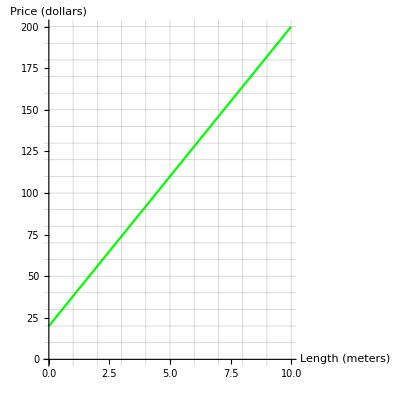

```mathematica
x="Length (meters)";y="Price (dollars)";x1=0; y1=20; x2=5;y2=110; x3=10; y3=200;
ListLinePlot[{{x1,y1},{x2,y2},{x3,y3}},GridLines->{
Range[0,10,1],
Range[0,200,10]},AxesStyle->Arrowheads[0.05],PlotStyle->Green,AxesLabel->{x,y},AspectRatio->1]
```

The price the first sawmill charges for each meter of wood is represented by the slope of the graph of p=5+20x. Since the formula for p is in slope-intercept form, we can determine that the slope is 20. This means that the first sawmill charges $20 for each meter of wood.

The price the second sawmill charges for each meter of wood is represented by the slope of the line on the graph. The line passes through the points (0,20) and (5,110). We can find its slope by taking the ratio of the corresponding differences in the y-values and the x-values of our two points:

```mathematica
(y2-y1)/(x2-x1)
```

18

This means that the second sawmill charges $18 for each meter of wood.

Since 20>18, the first sawmill charges more for each meter of wood.

Which sawmill has a cheaper price for a 5-meter wooden beam?

The price that the first sawmill charges for a 5-meter beam corresponds to the value of p when x=5:

```mathematica
p/.x->5
```

105

So the first sawmill charges $105 for a 5-meter beam.

The price that the second sawmill charges for a 5-meter beam corresponds to the point on the graph whose x-value is 5, which is (5,110). So the second sawmill charges $110 for a 5-meter beam.

Since 105<110, the first sawmill has a cheaper price for a 5-meter wooden beam.

### Julia and Kajal’s deliveries

Julia and Kajal make deliveries on their bicycles. For each delivery, they need some time to get ready, and then they each ride at a constant speed.

Julia takes 40 minutes to make a delivery 5 kilometers away. She uses 10 minutes of the delivery time to get ready.

The following equation gives the time it takes Kajal to make a delivery (in minutes) as a function of the distance of the delivery (in kilometers):

```mathematica
t=15+6d
```

15+6 d

Who takes more time to get ready?

We are given that Julia takes 10 minutes to get ready.

The time it takes Kajal to get ready corresponds to the value of t when d=0:

```mathematica
t/.d->0
```

15

This means Kajal takes 15 minutes to get ready.

Since 10<15, Kajal takes more time to get ready.

Who rides faster?

We are also given that Julia takes 40 minutes to make a delivery 5 kilometers away. Since she takes 10 minutes to get ready, we can conclude she rides 5 kilometers in 40−10=30 minutes. We can measure her speed by taking the ratio of the corresponding differences in time and distance:

```mathematica
30/5
```

6

This means that Julia rides one kilometer in 6 minutes.

The time it takes Kajal to ride one kilometer is represented by the slope of the graph of t = 15+6d. Since the formula for t is in slope-intercept form, we can determine that the slope is 6. This means that Kajal rides one kilometer in 6 minutes.

Since 6=6, they both ride at the same speed.

### Two young sumo wrestlers

Two young sumo wrestlers decided to go on a special diet to gain weight rapidly. They each gained weight at a constant rate.

The weight (in kilograms) of the first wrestler as a function of time (in months) is given by the following table of values:

```mathematica
x="Time (months)";y="Weight (kilograms)";x1=3; x2=4.5; x3=6;y1=95; y2=101.75; y3=108.5;
Grid[{{x,y},{x1,y1},{x2,y2},{x3,y3}},Spacings->{2,1},Frame->All,ItemStyle->"Text",Background->{{Magenta,Yellow},{Cyan,None}}]
```

Time (months) | Weight (kilograms)
3 | 95
4.5 | 101.75
6 | 108.5

The graph of the weight (in kilograms) of the second wrestler as a function of time (in months) is shown below.

Which wrestler weighed more at the beginning of the diet?

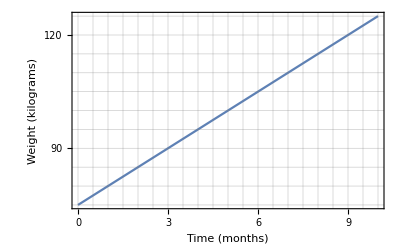

```mathematica
x="Time (months)";y="Weight (kilograms)";x1=0; y1=75; x2=5;y2=100; x3=10; y3=125;
ListLinePlot[{{x1,y1},{x2,y2},{x3,y3}},GridLines->{
Range[0,10,0.5],
Range[0,130,5]},Frame->True,FrameTicks->{{Range[0,130,10],None},{Range[0,10,1],None}},FrameLabel->{x,y}]
```

Which wrestler gained weight faster?

The table of values for the first wrestler shows that for each decrease of Time by 1.5 months, Weight decreases by 6.75 kilograms. We can extend the table according to this rate to find the value of Weight when Time was 0 months:

```mathematica
x="Time";y="Weight";x1=0; x2=1.5; x3=3;x4=4.5;x5=6;y1=81.5; y2=88.25; y3=95;y4=101.75;y5=108.5;
Grid[{{x,y},{x1,y1},{x2,y2},{x3,y3},{x4,y4},{x5,y5}},Spacings->{2,1},Frame->All,ItemStyle->"Text",Background->{{Magenta,Yellow},{Cyan,None}}]
```

Time | Weight
0 | 81.5
1.5 | 88.25
3 | 95
4.5 | 101.75
6 | 108.5

This means that the first wrestler weighed 81.5 kilograms at the beginning of the diet.

The weight of the second wrestler at the beginning of the diet is represented by the y-intercept of the line, which is (0,75). This means that the second wrestler weighed 75 kilograms at the beginning of the diet.

Since 81.5>75, the first wrestler weighed more at the beginning of the diet.

The rate at which the first wrestler gained weight is the ratio of the corresponding differences in Weight and Time:

```mathematica
-6.75/-1.5
```

4.5

This means that the first wrestler gained weight at a rate of 4.5 kilograms per month.

The rate at which the second wrestler gained weight is represented by the slope of the line. In addition to (0,75), the line passes through the point (1,80). We can find its slope by taking the ratio of the corresponding differences in the y-values and the x-values of our two points:

```mathematica
(80-75)/(1-0)
```

5

This means that the second wrestler gained weight at a rate of 5 kilograms per month.

Since 4.5 < 5, the second wrestler gained weight faster.

### Saskatchewan and Manitoba Widgets

Saskatchewan Widgets and Manitoba Widgets are two companies that were founded at the same time.

Saskatchewan Widgets started 10 million dollars in debt, and they make a constant yearly profit. After 5 years, they were 6 million dollars in debt.

The graph of the balance (in millions of dollars) of Manitoba Widgets as a function of time (in years) is shown below.

Which company started with a greater balance?

Which company makes a greater yearly profit?

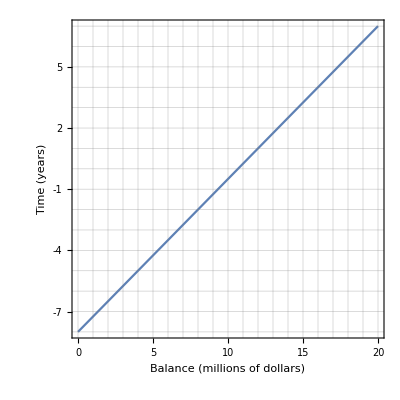

```mathematica
x="Balance (millions of dollars)";y="Time (years)";x1=0; y1=-8; x2=4;y2=-5; x3=20; y3=7;
ListLinePlot[{{x1,y1},{x2,y2},{x3,y3}},GridLines->{
Range[0,20,1],
Range[-10,10,1]},Frame->True,FrameTicks->{{Range[-10,10,1],None},{Range[0,20,1],None}},FrameLabel->{x,y},AspectRatio->1]
```

We are given that Saskatchewan started 10 million dollars in debt. In other words, the starting balance of the company was -10 million dollars.

Manitoba’s starting balance is represented by the y-intercept of the line, which is (0,-8). This means that the company’s starting balance was -8 million dollars.

Since -10 < -8, Manitoba had a greater starting balance.

We are given that after 5 years, Saskatchewan had -6 million dollars. We can find their yearly profit by taking the ratio of the corresponding differences in money and time:

```mathematica
(-6-(-10))/(5-0)
```

4/5

This means that Saskatchewan’s yearly profit is 4/5 million dollars (or $800,000).

The yearly profit Manitoba makes is represented by the slope of the line. In addition to (0,-8), the line passes through the point (4,-5). We can find its slope by taking the ratio of the corresponding differences in the y-values and the x-values of our two points:

```mathematica
(-5-(-8))/(4-0)
```

3/4

This means that Manitoba’s yearly profit is 3/4 million dollars (or $750,000).

Since 4/5>3/4 , Saskatchewan makes a greater yearly profit.

### Amira and Mandisa’s balloons

Amira and Mandisa sell balloon animals at different stands on the boardwalk. They each use a constant number of balloons per animal.

Amira started with a total of 260 balloons today, and she uses 4 balloons for each balloon animal she makes.

The remaining number of balloons in Mandisa’s stand as a function of the number of balloon animals she made today is given by the following table of values:

```mathematica
x="Animals";y="Balloons";x1=20; x2=40; x3=60;y1=225; y2=125; y3=25;
Grid[{{x,y},{x1,y1},{x2,y2},{x3,y3}},Spacings->{2,1},Frame->All,ItemStyle->"Text",Background->{{Magenta,Yellow},{Cyan,None}}]
```

Animals | Balloons
20 | 225
40 | 125
60 | 25

Who uses more balloons for each balloon animal?

We are given that Amira uses 4 balloons for each balloon animal she makes.

The table of values for Mandisa shows that for each increase of 20 in Animals, Balloons decreases by 100. The number of balloons Mandisa uses for each animal is the ratio of the corresponding differences in Balloons and Animals:

```mathematica
-100/20
```

-5

The rate of change is negative because each additional balloon animal made results in a decrease of 5 balloons in the number of remaining balloons. This means that Mandisa uses 5 balloons for each balloon animal she makes.

Since 4<5, Mandisa uses more balloons for each balloon animal she makes.

Both Amira and Mandisa used up all of their balloons. Who made more balloon animals?

We are given that Amira started with a total of 260 balloons today. Since she used all of them, and she uses 4 balloons for each animal she makes, we can conclude she made a total of 260/4=65 balloon animals today.

We can extend the table of Mandisa according to the rate of change we found to find the value of Animals when Balloons was 0:

```mathematica
x="Animals"; y="Balloons";x1=60; x2=61; x3=62; x4=63;x5=64; x6=65; y1=25; y2=20; y3=15; y4=10; y5=5; y6=0;
Grid[{{x,y},{x1,y1},{x2,y2},{x3,y3},{x4,y4},{x5,y5},{x6,y6}},Spacings->{2,1},Frame->All,ItemStyle->"Text",Background->{{Magenta,Yellow},{Cyan,None}}]
```

Animals | Balloons
60 | 25
61 | 20
62 | 15
63 | 10
64 | 5
65 | 0

This means that Mandisa made a total of 65 balloon animals today.

Since 65 = 65, they both made the same number of balloon animals.

### Red and blue hot-air balloons

Two hot-air balloons, one red and one blue, took off at the same time from different platforms. Each began ascending at a constant rate.

The following equation gives the height (in meters) of the red hot-air balloon as a function of time (in seconds).

```mathematica
h=1/2 t+4
```

4+t/2

The height (in meters) of the blue hot-air balloon as a function of time (in seconds) is given by the following table of values:

```mathematica
x="Time (seconds)";y="Height (meters)";x1=4; x2=6; x3=8;y1=5; y2=6; y3=7;
Grid[{{x,y},{x1,y1},{x2,y2},{x3,y3}},Spacings->{2,1},Frame->All,ItemStyle->"Text",Background->{{Magenta,Yellow},{Cyan,None}}]
```

Time (seconds) | Height (meters)
4 | 5
6 | 6
8 | 7

Which balloon started at a greater height?

The starting height of the red balloon corresponds to the value of h when t=0. To find it, all we need is to substitute t=0 into the formula for h:

```mathematica
h/.t->0
```

4

This means that the red balloon started at a height of 4 meters.

The table of values for the blue balloon shows that for each decrease of time by 2 seconds, height decreases by 1 meter. We can extend the table according to this rate to find the value of height when time was 0 seconds:

```mathematica
x="Time"; y="Height";x1=0; x2=2; x3=4; x4=6; x5=8;y1=3; y2=4; y3=5; y4=6; y5=7;
Grid[{{x,y},{x1,y1},{x2,y2},{x3,y3},{x4,y4},{x5,y5}},Spacings->{2,1},Frame->All,ItemStyle->"Text",Background->{{Magenta,Yellow},{Cyan,None}}]
```

Time | Height
0 | 3
2 | 4
4 | 5
6 | 6
8 | 7

This means that the blue balloon started at a height of 3 meters.

Since 4 > 3, the red balloon started from a greater height.

Which balloon ascended faster?

The rate at which the red balloon ascended is represented by the slope of the graph of h=1/2 t+4. Since the formula for h is in slope-intercept form, we can determine that the slope is 1/2. This means that the red balloon ascended at a rate of 1/2 meters per second.

The rate at which the blue balloon ascended is the ratio of the corresponding differences in height and time. This means that the blue balloon ascended at a rate of 1/2 meters per second.

Since 1/2=1/2, both balloons ascended at the same rate.

### Thor and Zeus’ hammers

Thor and Zeus strike with their hammers. The higher they raise their hammers before they strike, the louder the sound of the strike.

The following equation gives the loudness of Thor’s strike (in decibels) as a function of the height from which he strikes (in centimeters):

S=3h+25

The graph of the loudness of Zeus's strike (in decibels) as a function of the height from which he strikes (in centimeters) is shown below.

Whose loudness increases more per additional centimeter of height?

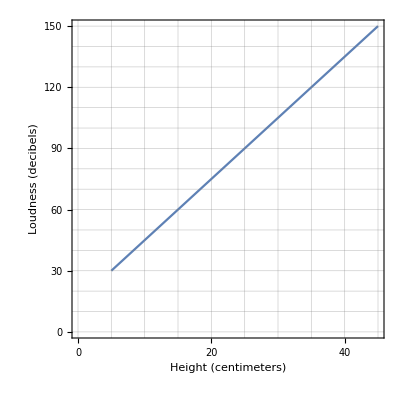

```mathematica
x="Height (centimeters)";y="Loudness (decibels)";x1=5; y1=30; x2=15;y2=60; x3=45; y3=150;
ListLinePlot[{{x1,y1},{x2,y2},{x3,y3}},GridLines->{
Range[0,50,5],
Range[0,200,10]},Frame->True,FrameTicks->{{Range[0,200,30],None},{Range[0,50,10],None}},FrameLabel->{x,y},AspectRatio->1]
```

#### Thor’s strike

The rate at which the loudness of Thor’s strike increases per additional centimeter of height is represented by the slope of the graph of S=3h+25. Since the formula for S is in slope-intercept form, we can determine that the slope is 3. This means that the loudness of Thor’s strike increases by 3 decibels per centimeter.

#### Zeus’ strike

The rate at which the loudness of Zeus's strike increases per additional centimeter of height is represented by the slope of the line on the graph. The line passes through the points (5,30) and (15,60). We can find its slope by taking the ratio of the corresponding differences in the y-values and the x-values of our two points:

```mathematica
m=(y2-y1)/(x2-x1)
```

3

This means that the loudness of Zeus’s strike increases by 3 decibels per centimeter.

Since 3=3, the increase in loudness per centimeter is the same for both.

Whose strike is louder when he strikes from a height of 40 centimeters?

The loudness of Thor’s strike from a height of 40 centimeters corresponds to the value of S when h=40. To find it, all we need is to substitute h=40 into the formula for S:

```mathematica
S=3h+25/.h->40
```

145

This means the loudness of Thor’s strike from a height of 440 centimeters is 145 decibels.

The loudness of Zeus’s strike from a height of 40 centimeters corresponds to the point on the line whose x-value is 40. The y-value of that point isn’t clearly visible, but it’s clear that it’s less than 140.

Therefore, Thor’s strike is louder when he strikes from a height of 40 centimeters.

#### Urpi's towels

Urpi wants to buy towels online. There are two stores with the kind of towel she wants.

The first store charges $20 per towel, and the delivery charge is $25.

The following equation gives the total price (in dollars) of an order from the second store (including delivery) as a function of the number of towels:

P=35+18n

Which store charges more per towel?

Urpi needs 15 towels. Which store is cheaper for her?

We are given that the first store charges $20 per towel.

The price the second store charges per towel is represented by the slope of the graph of P = 35 + 18n. Since the formula for P is in slope-intercept form, we can determine that the slope is 18. This means that the second store charges $18 per towel.

Since 20 > 18, the first store charges more per towel.

Since each towel at the first store costs $20, we know that 15 towels cost 15 ⋅ $20 = $300. We are also given that the store charges $25 for delivery. Therefore, the total price for 15 towels is $300 + $25 = $325.

The price of 15 towels in the second store corresponds to the value of P when n = 15. To find it, all we need is to substitute n = 15 into the formula for P:

```mathematica
P==35+18n/.n->15
```

P==305

This means that the total price for 15 towels in the second store is $305.

Since 325 > 305, the second store is cheaper for Urpi.

Nara's plants

Nara got two new plants for her apartment. Each plant grew at a constant rate.
The height (in centimeters) of the first plant as a function of time (in days since Nara got it) is given by the following table of values:

```mathematica
x="Time (days)";y="Height (centimeters)";x1=10; x2=15; x3=20;y1=34; y2=36; y3=38;
Grid[{{x,y},{x1,y1},{x2,y2},{x3,y3}},Spacings->{2,1},Frame->All,ItemStyle->"Text",Background->{{Magenta,Yellow},{Cyan,None}}]
```

Time (days) | Height (centimeters)
10 | 34
15 | 36
20 | 38

The graph of the height (in centimeters) of the second plant as a function of time (in days since Nara got it) is shown below.

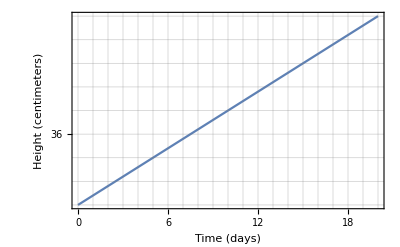

```mathematica
x1=0; y1=30; x2=10;y2=38; x3=20; y3=46;
ListLinePlot[{{x1,y1},{x2,y2},{x3,y3}},GridLines->{
Range[0,24,1],
Range[0,52,2]},Frame->True,FrameTicks->{{Range[0,52,4],None},{Range[0,24,2],None}},FrameLabel->{x,y}]
```

Which plant was taller when Nara got the plants?

Which plant grew faster?

The table of values for the first plant shows that for each decrease of Time by 5 days, Height decreases by 2 centimeters. We can extend the table according to this rate to find the value of Height when Time was 0 days:

```mathematica
x="Time";y="Height";x1=0; x2=5; x3=10; x4=15; x5=20; y1=30; y2=32; y3=34; y4=36; y5=38;
Grid[{{x,y},{x1,y1},{x2,y2},{x3,y3},{x4,y4},{x5,y5}},Spacings->{2,1},Frame->All,ItemStyle->"Text",Background->{{Magenta,Yellow},{Cyan,None}}]
```

Time | Height
0 | 30
5 | 32
10 | 34
15 | 36
20 | 38

This means that the first plant was 30 centimeters tall when Nara got it.

The height of the second plant when Nara got it is represented by the y-intercept of the line, which is (0,30). This means that the second plant was 30 centimeters tall when Nara got it.

Since 30 = 30, both plants were equally tall when Nara got them.

The rate at which the first plant grew is the ratio of the corresponding differences in Height and Time:

```mathematica
ΔHeight=-2;ΔTime=-5;
ΔHeight/ΔTime
```

2/5

This means that the first plant grew at a rate of 0.4 centimeters per day.

The rate at which the second plant grew is represented by the slope of the line. In addition to (0,30), the line passes through the point (10,38). We can find its slope by taking the ratio of the corresponding differences in the y-values and the x-values of our two points:

```mathematica
(38-30)/(10-0)
```

4/5

This means that the second plant grew at a rate of 0.8 centimeters per day.

Since 0.4 < 0.8, the second plant grew faster.

#### Jada and Alexandria’s spices

Jada and Alexandra sell spices at the marketplace. They each charge a constant price per kilogram of spices.

Jada has weekly expenses of $200. She covers her expenses and makes a profit of $280 for selling 80 kilograms of spices.

The graph of Alexandra’s weekly profit (in dollars) as a function of the amount of spices sold (in kilograms) is shown below.

Who has greater weekly expenses?

Who charges a greater price for one kilogram of spices?

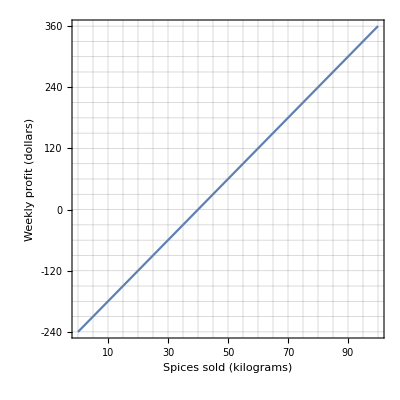

```mathematica
x1=0;y1=-240;x2=40;y2=0;x3=100;y3=360;
ListLinePlot[{{x1,y1},{x2,y2},{x3,y3}},GridLines->{
Range[0,100,5],
Range[-300,390,30]},Frame->True,FrameTicks->{{Range[-240,360,60],None},{Range[10,90,10],None}},FrameLabel->{"Spices sold (kilograms)","Weekly profit (dollars)"},AspectRatio->1]
```

We are given that Jada has weekly expenses of $200. In other words, her weekly profit is -$200 before she sells any spices.

Alexandra’s weekly expenses are represented by the y-intercept of the line, which is (0,-240). This means that Alexandra has weekly expenses of $240.

Since 200 < 240, Alexandra has greater weekly expenses.

We are given that Jada makes a profit of $280 for selling 80 kilograms of spices. We can find the price she charges for one kilogram of spices by taking the ratio of the corresponding differences in money and weight:

```mathematica
ΔMoney=280-(-200);ΔMass=80-0;
ΔMoney/ΔMass
```

6

This means that Jada charges $6 for one kilogram of spices.

The price Alexandra charges for one kilogram of spices is represented by the slope of the line. In addition to (0,-240), the line passes through the point (40,0). We can find its slope by taking the ratio of the corresponding differences in the y-values and the x-values of our two points:

```mathematica
(0-(-240))/(40-0)
```

6

This means that Alexandra charges $6 for one kilogram of spices.

Since 6 = 6, they charge the same price for one kilogram of spices.

The chess club and the ballet club of Nahk University were founded at the same time, and they each accept new members at a constant rate.

The chess club accepts 5 new members each week, and it had 37 members after 6 weeks.

The number of members in the ballet club as a function of time (in weeks) is given by the following table of values:

```mathematica
x=Time;y=Members;x1=3;x2=10;
x3=17;y1=28;y2=70;y3=112;
Grid[{{x,y},{x1,y1},{x2,y2},{x3,y3}},Spacings->{2,1},Frame->All,ItemStyle->"Text",Background->{{Gray,None},{LightGray,None}}]
```

Time | Members
3 | 28
10 | 70
17 | 112

Which club accepts more members each week?

Which club had more founding members?

We are given that the chess club accepts 5 new members each week.

The table of values for the ballet club shows that for each increase of 7 weeks of Time, Members increases by 42. The number of new members each week is the ratio of the corresponding differences in Members and Time:

```mathematica
ΔMembers=42;ΔTime=7;
ΔMembers/ΔTime
```

6

This means that the ballet club accepts 6 new members each week.

Since 5 < 6, the ballet club accepts more new members each week.

We are given that the chess club had 37 members after 6 weeks. Since they accept 5 new members each week, they accepted 6 ⋅ 5 = 30 new members since the club was founded. 37 - 30 = 7, so the chess club had 7 founding members.

We can extend the table of the ballet club according to the rate of change we found to find the value of Members when Time was 0 weeks:

```mathematica
x=Time;y=Members;x1=0;x2=1;
x3=2;x4=3;y1=10;y2=16;y3=22;y4=28;
Grid[{{x,y},{x1,y1},{x2,y2},{x3,y3},{x4,y4}},Spacings->{2,1},Frame->All,ItemStyle->"Text",Background->{{Gray,None},{LightGray,None}}]
```

Time | Members
0 | 10
1 | 16
2 | 22
3 | 28

This means that the ballet club had 10 founding members.

Since 7 < 10, the ballet club had more founding members.

Antoine wants to get a subscription to a local library. There are two libraries, each of which charges a monthly subscription fee plus a fee for each book loaned.

The following equation gives the monthly cost (in dollars) of joining the first library as a function of the number of books loaned.

```mathematica
c==10+1.5n
```

The monthly cost (in dollars) of the second library as a function of the number of books loaned is given by the following table of values:

```mathematica
x=Books;y=Price;x1=2;x2=8;
x3=14;y1=15.50;y2=26;y3=36.50;
Grid[{{x,y},{x1,y1},{x2,y2},{x3,y3}},Spacings->{2,1},Frame->All,ItemStyle->"Text"]
```

Books | Price
2 | 15.5
8 | 26
14 | 36.5

Which library charges more for each book loaned?

Which library has a cheaper subscription fee?

The fee that the first library charges for each book loaned is represented by the slope of the line of C. Since the formula for C is in slope-intercept form, we can determine that the slope is 1.5. This means that the first library charges $1.50 for each book loaned.

The table of values for the second library shows that for each increase of books by 6, cost increases by $10.50. The fee that the library charges for each book loaned is the ratio of the corresponding differences in cost and books:

```mathematica
Δcost=10.5;Δbooks=6
```

6

```mathematica
Δcost/Δbooks
```

1.75

This means that the second library charges $1.75 for each book loaned.

Since 1.5 < 1.75, the second library charges more for each book loaned.

The subscription fee of the first library corresponds to the value of C when n=0. To find it, all we need is to substitute n=0 into the formula for C:

```mathematica
c==10+1.5n/.n->0
```

c==10.

This means that the subscription fee of the first library is $10.

We can extend the table of the second library according to the rate of change we found to find the value of cost when books is 0:

```mathematica
x=Books;y=Price;x1=0;x2=1;
x3=2;y1=12;y2=13.75;y3=15.50;
Grid[{{x,y},{x1,y1},{x2,y2},{x3,y3}},Spacings->{2,1},Frame->All,ItemStyle->"Text",Background->{{Gray,None},{LightGray,None}}]
```

Books | Price
0 | 12
1 | 13.75
2 | 15.5

This means that the subscription fee of the second library is $12.

Since 10 < 12, the first library has a cheaper subscription fee.

Two stoves were turned off at the same time, and they both started to cool down.

The following equation gives the temperature of the first stove (in degrees Celsius) as a function of time (in minutes).

```mathematica
T==180-1.55m
```

The graph of the temperature of the second stove (in degrees Celsius) as a function of time (in minutes) is shown below.

Which stove started at a higher temperature?

Which stove cooled down at a greater rate?

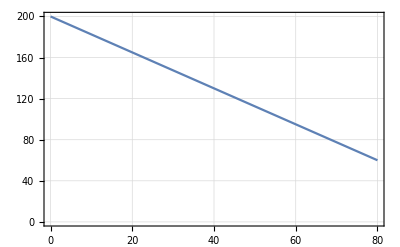

```mathematica
x1=0;y1=200;x2=40;y2=130;x3=80;y3=60;
ListLinePlot[{{x1,y1},{x2,y2},{x3,y3}},PlotTheme->"Detailed"]
```

The starting temperature of the first stove corresponds to the value of T when m=0. To find it, all we need is to substitute m=0 into the formula for T:

```mathematica
T==180-1.55m/.m->0
```

T==180.

This means that the first stove started at a temperature of 180∘ Celsius.

The starting temperature of the second stove corresponds to the line’s y-intercept, which is (0,200). This means that the second stove started at a temperature of 200∘ Celsius.

Since 180 < 200, the second stove started at a higher temperature.

The rate at which the first stove changed temperature is represented by the slope of the line of T. Since the formula for T is in slope-intercept form, we can determine that the slope is -1.55. The slope is negative, so the temperature was decreasing. Decreasing in temperature by a certain number of degrees is the same as cooling down by that number of degrees. So the slope means that the first stove cooled down at a rate of 1.55∘ Celsius per minute.

The rate at which the second stove changed temperature is represented by the slope of the line on the graph. In addition to (0,200), the line passes through the point (40,130). We can find its slope by taking the ratio of the corresponding differences in the y-values and the x-values of our two points:

```mathematica
(130-200)/(40-0)
```

-7/4

This means that the second stove cooled down at a rate of 1.75∘ Celsius per minute.

Since 1.55 < 1.75, the second stove cooled down faster.

Christov and Mateus gave out candy to children on Halloween. They each gave out candy at a constant rate, and they both gave away all of their candy.

Christov initially had 300 pieces of candy, and after he was visited by 17 children, he had 249 pieces left.

The following equation gives the number of remaining pieces of candy Mateus had as a function of the number of children who visited him:

```mathematica
M==270-3n
```

Who gave more candy to each child who visited him?

Who gave candy to a greater number of children?

We are given that Christov initially had 300 pieces of candy, and after he was visited by 17 children, he had 249 pieces left. Since 300-249=51, we know Christov gave 51 pieces to 17 children. Therefore, he gave 51/17= 3 pieces to each child.

The slope of the graph of M=270-3n shows us how much the number of pieces of candy Mateus had changed with each child to whom he gave candy. Since the formula for M is in slope-intercept form, we can determine that the slope is -3. The slope is negative because each additional child resulted in a decrease of 3 pieces of candy. This means that Mateus gave 3 pieces to each child.

Since 3=3, they both gave out the same number of pieces of candy per child.

We know that Christov initially had 300 pieces of candy and that he gave 3 pieces to each child. Therefore, he gave candy to a total of 300/3=100 children.

The total number of children to whom Mateus gave candy corresponds to the value of n when M=0. We can find it by using the formula for M and solving the resulting equation:

```mathematica
Solve[M=0;270-3n==0]
```

{{n→90}}

This means Mateus gave candy to a total of 90 children.

Since 100 > 90, Christov gave candy to a greater number of children.

Devora tested two engines. As each engine’s rotation got faster, its temperature increased at a constant rate.

The first engine’s temperature (in degrees Celsius) as a function of its rotation speed (in cycles per second) is given by the following table of values:

```mathematica
x=Rotation;y=Temperature;x1=8;x2=11;
x3=14;y1=26.4;y2=28.8;y3=31.2;
Grid[{{x,y},{x1,y1},{x2,y2},{x3,y3}},Spacings->{2,1},Frame->All,ItemStyle->"Text"]
```

Rotation | Temperature
8 | 26.4
11 | 28.8
14 | 31.2

The graph of the second engine’s temperature (in degrees Celsius) as a function of its rotation speed (in cycles per second) is shown below.

The temperature of which engine increased more for each increase of 1 cycle per second?

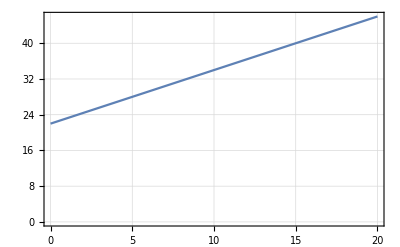

```mathematica
x1=0;y1=22;x2=10;y2=34;x3=20;y3=46;
ListLinePlot[{{x1,y1},{x2,y2},{x3,y3}},PlotTheme->"Detailed"]
```

The table of values for the first engine shows that for each increase of Rotation by 3 cycles per second, Temperature increases by 2.4 degrees Celsius. The increase in temperature for each increase of 1 cycle per second is the ratio of the corresponding differences in Temperature and Rotation:

```mathematica
ΔRotation=2.4;
ΔTemperature=3
```

3

```mathematica
ΔRotation/ΔTemperature
​
```

0.8

This means that the first engine’s temperature increased by 0.8 degrees Celsius for each increase of 1 cycle per second.

The second engine’s increase in temperature for each increase of 1 cycle per second is represented by the slope of the line. The line passes through the points (0,22) and (5,28). We can find its slope by taking the ratio of the corresponding differences in the y-values and the x-values of our two points:​

```mathematica
(28-22)/(5-0)
```

6/5

This means that the second engine’s temperature increased by 1.2 degrees Celsius for each increase of 1 cycle per second.

Since 0.8 < 1.2, the second engine’s temperature increased more for each increase of 1 cycle per second.

We can extend the table according to the rate of change it exhibits to find the value of Temperature when Rotation was 20 cycles per second:

```mathematica
x=Rotation;y=Temperature;x1=8;x2=11;
x3=14;x4=17;x5=20;y1=26.4;y2=28.8;y3=31.2;y4=33.6;y5=36;
Grid[{{x,y},{x1,y1},{x2,y2},{x3,y3},{x4,y4},{x5,y5}},Spacings->{2,1},Frame->All,ItemStyle->"Text"]
```

Rotation | Temperature
8 | 26.4
11 | 28.8
14 | 31.2
17 | 33.6
20 | 36

This means that the first engine’s temperature was 36 degrees Celsius when it rotated at 20 cycles per second.

The temperature of the second engine when it rotated at 20 cycles per second is represented by the point on the line whose x-coordinate is 20, which is (20,46). This means that the second engine’s temperature was 46 degrees Celsius when it rotated at 20 cycles per second.

Since 36 < 46, the second engine was hotter when it rotated at 20 cycles per second.

Sean and Mariana started drinking their slushies at the same time and tried to drink them as fast as they could.

Sean started with 300 milliliters of slushy, and he drank 5.5 milliliters per second.
The graph of the remaining volume of slushy in Mariana’s cup (in milliliters) as a function of time (in seconds) is shown below.
Who drank their slushy faster?

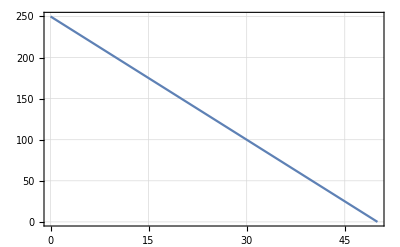

```mathematica
x1=0;y1=250;x2=50;y2=0;
ListLinePlot[{{x1,y1},{x2,y2}},PlotTheme->"Detailed"]
```

We are given that Sean drank his slushy at a rate of 5.5 milliliters per second.

The rate at which Mariana drank her slushy is represented by the slope of the line. We can see the line passes through the points (0,250) and (10,200). We can find its slope by taking the ratio of the corresponding differences in the y-values and the x-values of our two points:

```mathematica
(200-250)/(10-0)
```

-5

The slope is negative because each additional second resulted in a decrease of 5 milliliters. This means that Mariana drank at a rate of 5 milliliters per second.

Since 5.5 > 5, Sean drank his slushy faster.

We are given that Sean initially had 300 milliliters of slushy. The time it took him to finish the slushy can be found by dividing that amount by the rate at which he drank:

```mathematica
volume=300;Rate=5.5
```

5.5

```mathematica
Time==volume/Rate
```

Time==54.5455

The time at which Mariana finished her slushy corresponds to the graph’s x-intercept, which is (50,0). This means that Mariana finished her slushy after 50 seconds.

Since 54 6/11 > 50, Mariana finished drinking her slushy first.